```mathematica
filenames={"timing_adjmat.txt","timing_adjlst_2.txt","timing_adjlst_4.txt","timing_adjlst_5.txt","timing_adjlst_10.txt"};
```

```mathematica
data=Map[Mean[Partition[N@Import["/home/tm/Projects/teatime_presentation/misc/files/"<>#,"Table"],11]][[All,{1,-1}]]&,filenames]
```

{{{100.,0.666667},{200.,3.66667},{400.,15.3333},{600.,43.},{800.,82.6667},{1000.,160.667},{2000.,831.},{4000.,4305.},{6000.,10137.7},{8000.,24861.7},{10000.,42171.7}},{{100.,0.},{200.,2.33333},{400.,10.},{600.,20.},{800.,48.6667},{1000.,92.3333},{2000.,569.},{4000.,3387.67},{6000.,8839.33},{8000.,17999.7},{10000.,28143.7}},{{100.,0.},{200.,1.33333},{400.,4.66667},{600.,14.6667},{800.,32.},{1000.,47.3333},{2000.,291.333},{4000.,1714.33},{6000.,4790.67},{8000.,8417.},{10000.,16645.7}},{{100.,0.},{200.,1.},{400.,4.},{600.,10.6667},{800.,24.6667},{1000.,38.},{2000.,210.333},{4000.,1294.67},{6000.,3581.33},{8000.,7986.},{10000.,13479.3}},{{100.,0.},{200.,0.666667},{400.,1.66667},{600.,6.33333},{800.,9.33333},{1000.,20.3333},{2000.,112.667},{4000.,659.},{6000.,1886.33},{8000.,3828.},{10000.,6395.67}}}

```mathematica
xl=Row[{Style["Number of vertices ",FontFamily->"Latin Modern Roman",Plain,18],Style["N",FontFamily->"Latin Modern Roman",Italic,18],Style[" [m]",FontFamily->"Latin Modern Roman",Plain,18]}]
```

Number of vertices N [m]

```mathematica
yl=Row[{Style["Runtimes ",FontFamily->"Latin Modern Roman",Plain,18],
DisplayForm[Row[{SubscriptBox[Style["t",FontFamily->"Latin Modern Roman",Italic,18],Style["t3nsor",FontFamily->"Latin Modern Roman",Plain,12]],Style["(N)",FontFamily->"Latin Modern Roman",Italic,18]}]],
Style[" [ms]",FontFamily->"Latin Modern Roman",Plain,18]}]
```

Runtimes t_t3nsor(N) [ms]

```mathematica
pl[Nnearrat_]:=Row[{DisplayForm[Style["N/",16,FontFamily->"Latin Modern Roman",Italic]],
DisplayForm@SubscriptBox[Style["N",FontFamily->"Latin Modern Roman",Italic,16],Style["near",FontFamily->"Latin Modern Roman",Plain,12]],Style["="<>ToString[Nnearrat],FontFamily->"Latin Modern Roman",Plain,16]}];
```

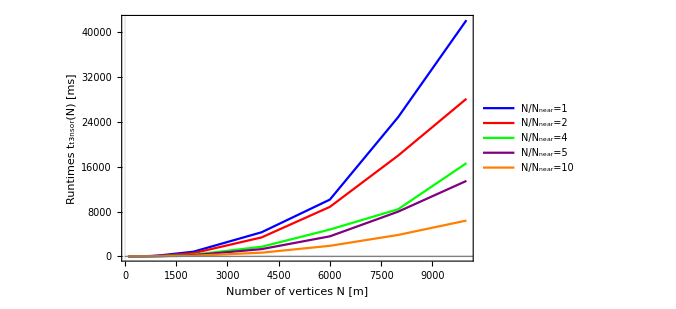

```mathematica
g=ListLinePlot[
data,
PlotStyle->{Blue,Red,Green,Purple,Orange},
PlotRange->All,
ColorFunctionScaling->False,
PlotTheme->"Scientific",
FrameStyle->Directive[Black,FontColor->Black,15,FontFamily->"Latin Modern Roman",Plain],
FrameLabel->{xl,yl},
ImageSize->{500,500./GoldenRatio},
PlotRangePadding->0,
PlotLegends->Placed[LineLegend[Automatic,{pl[1],pl[2],pl[4],pl[5],pl[10]},LegendLayout->"Column"],{1/6,0.7}],
Epilog->{Gray,Line[{{0,1},{10^5,1}}]}
]
```

```mathematica
Export["/home/tm/Projects/teatime_presentation/images/ha_t3nsor_runtimes_absolute.png",g,ImageResolution->500];
```

```mathematica
data2=Map[{data[[1,All,1]],#}ᵀ&,Map[data[[1,All,2]]/(0.00000000001+#)&,data[[All,All,2]]]/{1,2,4,5,10}];
```

```mathematica
xl=Row[{Style["Number of vertices ",FontFamily->"Latin Modern Roman",Plain,18],Style["N",FontFamily->"Latin Modern Roman",Italic,18],Style[" [m]",FontFamily->"Latin Modern Roman",Plain,18]}]
yl=Row[{Style["Efficiency ",FontFamily->"Latin Modern Roman",Plain,18],
DisplayForm[Row[{Style["ϵ",FontFamily->"Latin Modern Roman",Plain,21],Style["(N)",FontFamily->"Latin Modern Roman",Italic,18]}]],Style[" [1]",FontFamily->"Latin Modern Roman",Plain,18]}]
pl[Nnearrat_]:=Row[{DisplayForm[Style["N/",16,FontFamily->"Latin Modern Roman",Italic]],
DisplayForm@SubscriptBox[Style["N",FontFamily->"Latin Modern Roman",Italic,16],Style["near",FontFamily->"Latin Modern Roman",Plain,12]],Style["="<>ToString[Nnearrat],FontFamily->"Latin Modern Roman",Plain,16]}];
```

Number of vertices N [m]

Efficiency ϵ(N) [1]

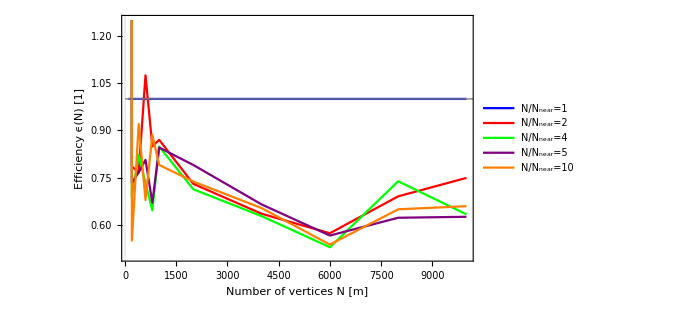

```mathematica
g=ListLinePlot[
data2,
PlotStyle->{Blue,Red,Green,Purple,Orange},
PlotRange->{All,{0.5,1.25}},
ColorFunctionScaling->False,
PlotTheme->"Scientific",
FrameStyle->Directive[Black,FontColor->Black,15,FontFamily->"Latin Modern Roman",Plain],
FrameLabel->{xl,yl},
ImageSize->{500,500./GoldenRatio},
PlotRangePadding->0,
PlotLegends->Placed[LineLegend[Automatic,{pl[1],pl[2],pl[4],pl[5],pl[10]},LegendLayout->"Column"],{5/6,0.7}],
Epilog->{Gray,Thin,Line[{{0,1},{10^5,1}}]}
]
```

```mathematica
Export["/home/tm/Projects/teatime_presentation/images/ha_t3nsor_runtimes_efficiency.png",g,ImageResolution->500];
```